# Učení RBF sítě Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují dva dobře oddělené shluky dat, každý shluk reprezentuje jednu třídu.
Vygenerujeme tedy tyto dva shluky dat.

```mathematica
values=50;
cluster1 =RandomReal[{-2,1},{values,2}];
cluster2=RandomReal[ {9,12},{values,2}];
inData = Join[cluster1,cluster2];
outcluster1=ConstantArray[{1,0},{values}];
outcluster2 = ConstantArray[{0,1},{values}];
outData= Join[outcluster1,outcluster2];
```

Takto vypadají naše vynerovaná vstupní data.

```mathematica
inData
```

{{-0.0912691,-0.565367},{0.427326,-1.07753},{0.965279,-0.416518},{-1.80933,0.651781},{0.806891,-0.585959},{-0.439959,-1.91227},{0.903715,-1.66379},{0.24878,0.158305},{-1.39258,-1.32112},{-0.536791,-1.57707},{0.810941,0.743338},{-0.745726,0.0504046},{-1.72991,-1.35279},{0.543265,0.979351},{-1.90478,0.291414},{-1.90369,-1.27167},{-1.40418,0.69159},{0.462333,-0.971484},{0.147266,0.262178},{0.876385,-1.40577},{-1.11804,0.816688},{-1.64841,-0.934559},{-0.96535,-0.569716},{-1.85866,-1.58084},{-1.58811,-0.540278},{-0.519346,-1.98732},{-0.0972039,-1.52825},{0.0365757,-1.87624},{0.50631,-0.348278},{-0.0954255,0.285007},{-1.68955,-0.900938},{-0.968714,-1.31812},{-0.547125,-1.4595},{-0.292276,0.57906},{-1.1287,-1.09986},{0.337814,-1.73004},{-1.01597,-0.720309},{0.115768,-1.8386},{-1.36216,-0.812241},{-0.169032,0.297854},{-1.19655,-1.71585},{0.801942,-0.986875},{-1.89259,-1.76684},{-1.73654,-0.680797},{0.825208,-1.48277},{-1.73318,-0.779979},{-1.46018,-1.80959},{-1.59806,0.189972},{-1.22884,-0.0517134},{-1.45043,-1.96229},{10.2305,11.8211},{9.08442,9.20022},{10.5671,11.5692},{9.52759,11.1847},{11.5504,10.5906},{10.2287,10.7002},{10.4909,11.1358},{11.4435,9.61829},{9.92985,9.08504},{9.14721,10.1657},{11.3622,11.5532},{9.70301,10.3733},{11.9309,10.0891},{11.3286,11.8521},{10.5682,10.0552},{9.37107,11.7386},{9.19548,11.8679},{11.9316,10.0084},{11.0897,10.0881},{11.4942,11.1107},{9.54774,10.1258},{11.0542,9.49159},{10.6636,10.9006},{10.3624,10.3173},{9.86822,9.03443},{10.7941,9.22523},{10.6904,10.801},{10.1067,9.81557},{10.1629,9.60071},{11.8939,9.63731},{11.659,9.47229},{9.70556,9.54512},{9.49292,10.647},{11.8777,9.77725},{11.6106,10.3684},{11.2357,11.7594},{10.3665,11.0993},{10.0214,9.04166},{9.21986,9.49422},{9.35908,11.0398},{10.7241,9.19481},{9.30324,11.2294},{9.17917,11.7755},{10.3491,11.2899},{11.8848,10.2247},{10.5736,9.78488},{10.6684,9.44527},{11.3871,11.1045},{11.4841,9.00757},{11.2933,11.1695}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme zobrazit pro lepší představu zobrazit. Každá třída dat má v grafu jinou bavu.

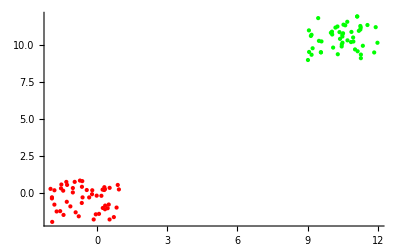

```mathematica
ListPlot[{cluster1,cluster2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě s jedním RBF neuronem, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,1, OutputNonlinearity->Sigmoid,RandomInitialization->True]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 15, 21, 2, 5.8563153}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-15 at 21:00. The network has 2 inputs and 2 outputs.  It consists of 1 basis function of Exp type. The network has a linear submodel. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

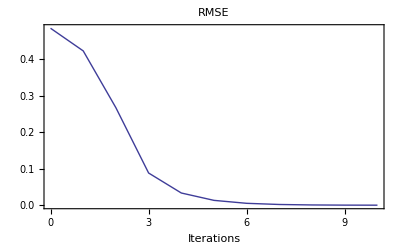

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Podívejme se jak naše síť klasifikuje data.

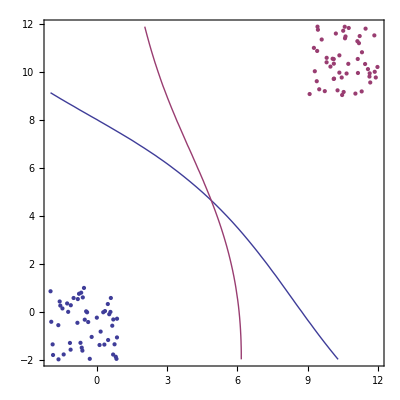

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronu

Nyní se podíváme na “vnitřnosti” neuronové sítě. Naše síť obsahuje jeden RBF neuron, mohlo by být zajímavé zjistit jakou oblast dat tento neuron pokrývá.
Nejprve upravíme síť aby vracela námi požadovaný výstup.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[1],{0}];(*změna matice vah na identidkou matici*)
net3=NeuronDelete[net3,{0,0}];(*odstranění lineární části*)
```

A zobrazíme výstup.

```mathematica
gauss=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All]
```

-Graphics3D-

Ještě přidáme do grafu vstupní data - kraf se otáčí pomocí levého tlačítka myši, vstupní data jsou vidět zespodu.

```mathematica
cluster13d=cluster1/.{x_?NumberQ,y_?NumberQ}->{x,y,0.501};
cluster23d=cluster2/.{x_?NumberQ,y_?NumberQ}->{x,y,0.501};
data3d=ListPointPlot3D[{cluster13d,cluster23d},PlotStyle->{Red,Green},PlotStyle->PointSize[Large]];
Show[gauss,data3d]
```

-Graphics3D-